# The Mobile 3rd Space

## Declare Base Constants

## Declare Thermal Resistances

## Equations

```mathematica
eqn2={C1 Ttile'[t]==Q-(Ttile[t]-Twall[t])/Reff,C2 Twall'[t]==(Ttile[t]-Twall[t])/Reff-(Twall[t]-Tout)/R4,Ttile[0]==10,Twall[0]==10}
```

{C1 Ttile'[t]==Q-(Ttile[t]-Twall[t])/Reff,C2 Twall'[t]==(Ttile[t]-Twall[t])/Reff-(-Tout+Twall[t])/R4,Ttile[0]==10,Twall[0]==10}

```mathematica
sol=DSolveValue[eqn2,{Ttile[t],Twall[t]},t]
```

{-(2 ⅇ^-1 Reff^2 (10 C1^3 C2 ⅇ^(((5+√1) t)/(C1 C2 R4 Reff^2)) R4^3 Reff+20 C1^2 C2^2 ⅇ^(1/1) R4^3 Reff+152+C1^2 C2 ⅇ^(1/1+1) R4 Reff √(-4 C1 C2 R4 Reff^3+(C1 R4 Reff+C2 R4 Reff+C1 Reff^2)^2) Tout))/((C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2+2 C1^2 R4 Reff-2 C1 C2 R4 Reff+C1^2 Reff^2) (-C1 R4 Reff-C2 R4 Reff-C1 Reff^2+√(-4 C1 C2 R4 Reff^3+(1)^2)) (C1 R4 Reff+C2 R4 Reff+C1 Reff^2+√(-4 C1 C2 R4 Reff^3+(C1 R4 Reff+C2 R4 Reff+C1 Reff^2)^2))),-1}
 |  |  |  |

```mathematica
tileTemp=sol⟦1⟧;
wallTemp=sol⟦2⟧;
airTemp[t_,Reff]=wallTemp+((tileTemp-wallTemp)(Reff-R1))/Reff
```

-((2 2 (10 C1^3 C2 ⅇ^(((5+√1) t)/(C1 C2 R4 Reff^2)) R4^3 Reff+20 C1^2 C2^2 ⅇ^(1/1) R4^3 Reff+126+C1^2 C2 4 Tout-C1^2 C2 ⅇ^(1/1+1) R4 Reff √(-4 C1 C2 R4 Reff^3+(C1 R4 Reff+C2 R4 Reff+C1 Reff^2)^2) Tout))/((C1^2 R4^2+2 C1 C2 R4^2+C2^2 R4^2+2 C1^2 R4 Reff-2 C1 C2 R4 Reff+C1^2 Reff^2) (-C1 R4 Reff-C2 R4 Reff-C1 Reff^2+√(-4 C1 C2 R4 Reff^3+(1)^2)) (C1 R4 Reff+C2 R4 Reff+C1 Reff^2+√(-4 C1 C2 R4 Reff^3+(C1 R4 Reff+C2 R4 Reff+C1 Reff^2)^2))))+((1) 1)/Reff
 |  |  |  |

## Calculate Thermal Resistances

```mathematica
r1=1/(30 14.8645)(* Thermal Mass *)
r2=1/(30  71.3495)(* Wall -> air inside *)
r3=0.15/(0.02  71.3495)(* Conduction through wall *)
r4=1/(35 71.3495) (* Wall -> air outside *)
Ref=r1+r2+r3
```

0.00224248

0.000467184

0.105116

0.000400443

0.107826

## Plotting

```mathematica
(*flux = -0.361*Cos[(t*Pi)/(12*3600)]+0.2243*Cos[(t*Pi)/(6*3600)]+0.2097*)
```

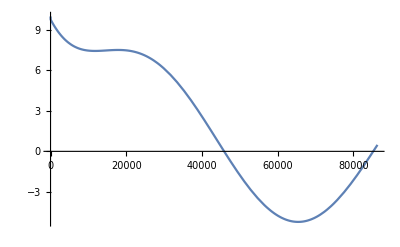

```mathematica
Plot[airTemp[t,Reff]/.{R1->0.002242479285097604,R4->0.00040044329072283014,Reff->0.10782602693901715,C1->200*800,C2->100*100,C3->9,Q->-0.361*Cos[(t*Pi)/(12*3600)]+0.2243*Cos[(t*Pi)/(6*3600)]+0.2097,Tout-> -3+6*Sin[(2*Pi*t)/(24*60*60)]+((3*Pi)/(4)),C[1]->4},{t,0,86400}]
```

## Solve Take 2

## Solving